```mathematica
{x1,x2}.({{A11, A12}, {A21, A22}}).{x1,x2}//Expand
```

A11 x1^2+A12 x1 x2+A21 x1 x2+A22 x2^2

```mathematica
D[{x1,x2}.({{A11, A12}, {A21, A22}}).{x1,x2},{{x1,x2}}]
```

{2 A11 x1+A12 x2+A21 x2,A12 x1+A21 x1+2 A22 x2}

```mathematica
x^2+y^2+ρ x y/.{x->1,y->1}
```

2+ρ

```mathematica
PDF[MultinormalDistribution[{0,0},({{1, ρ}, {ρ, 1}})],{x1,x2}]//FullSimplify
```

(ⅇ^((x1^2+x2^2-2 x1 x2 ρ)/(2 (-1+ρ^2))))/(2 π √(1-ρ^2))

```mathematica
Manipulate[
Plot3D[(x^2+y^2-ρ x y)/(2(1-ρ^2)),{x,-1,1},{y,-1,1}],
{ρ,-1,1}]
```

```mathematica
Solve[{a+b==1,a-b==-ρ},{a,b}]
```

{{a→(1-ρ)/2,b→(1+ρ)/2}}

```mathematica
FullSimplify[
Solve[{ξ1==√((1-ρ)/2)(x1+x2),ξ2==√((1+ρ)/2)(x1-x2)},{x1,x2}],
-1<ρ<1]
```

{{x1→(ξ2 √(1-ρ)+ξ1 √(1+ρ))/(√(2-2 ρ^2)),x2→(-ξ2 √(1-ρ)+ξ1 √(1+ρ))/(√(2-2 ρ^2))}}

```mathematica
(-(c Sin[θ])/(√(2(1-ρ)))+(c Cos[θ])/(√(2(1+ρ))))^2+(-(c Sin[θ])/(√(2(1-ρ)))-(c Cos[θ])/(√(2(1+ρ))))^2//FullSimplify
```

(c^2 (-1+ρ Cos[2 θ]))/(-1+ρ^2)

```mathematica
Solve[{(c Cos[θ])/(√(2(1-ρ)))-(c Sin[θ])/(√(2(1+ρ)))==x},θ,InverseFunctions->True]//FullSimplify
```

{{θ→-ArcCos[(c x √(1-ρ) (1+ρ)-√(-c^2 (-1+ρ) (c^2+x^2 (-1+ρ^2))))/(√2 c^2)]},{θ→ArcCos[(c x √(1-ρ) (1+ρ)-√(-c^2 (-1+ρ) (c^2+x^2 (-1+ρ^2))))/(√2 c^2)]},{θ→-ArcCos[(c x √(1-ρ) (1+ρ)+√(-c^2 (-1+ρ) (c^2+x^2 (-1+ρ^2))))/(√2 c^2)]},{θ→ArcCos[(c x √(1-ρ) (1+ρ)+√(-c^2 (-1+ρ) (c^2+x^2 (-1+ρ^2))))/(√2 c^2)]}}

```mathematica
Solve[{(c Cos[θ])/(√(2(1-ρ)))+(c Sin[θ])/(√(2(1+ρ)))==a},θ]//FullSimplify
```

{{θ→-ArcCos[(a c √(1-ρ) (1+ρ)-√(-c^2 (-1+ρ) (c^2+a^2 (-1+ρ^2))))/(√2 c^2)]},{θ→ArcCos[(a c √(1-ρ) (1+ρ)-√(-c^2 (-1+ρ) (c^2+a^2 (-1+ρ^2))))/(√2 c^2)]},{θ→-ArcCos[(a c √(1-ρ) (1+ρ)+√(-c^2 (-1+ρ) (c^2+a^2 (-1+ρ^2))))/(√2 c^2)]},{θ→ArcCos[(a c √(1-ρ) (1+ρ)+√(-c^2 (-1+ρ) (c^2+a^2 (-1+ρ^2))))/(√2 c^2)]}}

```mathematica
Module[{ρ=1/2,a1=1/2,b1=4/5,a2=4/5,b2=1},
N[Integrate[1/(2π √(1-ρ^2))Exp[-(x^2+y^2-2ρ x y)/(2(1-ρ^2))]x,{x,a1,b1},{y,a2,b2}],50]]
```

0.0046126949537664441869944804609273171000583354280445

```mathematica
0.027524624870300725f
```

```mathematica
Module[{plot,c=0.5,ρ=-0.65},
plot=ContourPlot[x^2+y^2-2ρ x y==c,{x,-1,1},{y,-1,1},PlotPoints->30,
Epilog->{Thick,Dashed,
Line[{{0,0},{√(c/(2(1+ρ))),-√(c/(2(1+ρ)))}}],
Text["√(c/(1 + ρ))",{0.5 √(c/(2(1+ρ))),-0.8 √(c/(2(1+ρ)))}],
Line[{{0,0},{√(c/(2(1-ρ))),√(c/(2(1-ρ)))}}],Text["√(c/(1 - ρ))",{0.4 √(c/(2(1-ρ))),0.9 √(c/(2(1-ρ)))}]
}];
Export[NotebookDirectory[]<>"../fig/ellipse.pdf",plot]]
```

/home/cossio/Jl/TruncatedNormal/mathematica/../fig/ellipse.pdf

```mathematica
Norm[{√(c/(2(1-ρ))),√(c/(2(1-ρ)))}]
```

√Abs[c/(1-ρ)]

```mathematica
c/(1-ρ)-c/(1+ρ)//FullSimplify
```

-(2 c ρ)/(-1+ρ^2)

```mathematica
(c/(1-ρ))^2-(c/(1+ρ))^2//FullSimplify
```

(4 c^2 ρ)/((-1+ρ^2)^2)

```mathematica
(c/(1+ρ))^2+(c/(1-ρ))^2//FullSimplify
```

(2 c^2 (1+ρ^2))/((-1+ρ^2)^2)

```mathematica
NotebookDirectory[]
```

/home/cossio/Jl/TruncatedNormal/mathematica/

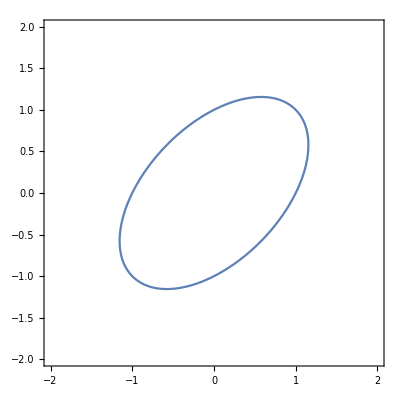

```mathematica
Module[{ρ=0.5,c=1},
ParametricPlot[{√(1/2 c/(1-ρ))Cos[t]+√(1/2 c/(1+ρ))Sin[t],√(1/2 c/(1-ρ))Cos[t]-√(1/2 c/(1+ρ))Sin[t]},{t,0,2π},PlotPoints->30,PlotRange->{{-2,2},{-2,2}},Frame->True]]
```

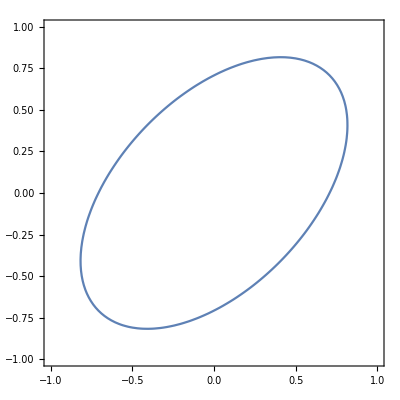

```mathematica
Module[{ρ=0.5,c=0.5},
ContourPlot[x^2+y^2-2ρ x y==c,{x,-1,1},{y,-1,1},PlotPoints->30]]
```

```mathematica
x1^2+x2^2-2ρ x1 x2/.{x1->1/(√2)(ξ1+ξ2),x2->1/(√2)(ξ1-ξ2)}//FullSimplify
```

-ξ1^2 (-1+ρ)+ξ2^2 (1+ρ)

```mathematica
Integrate[Exp[-x^2/2] x^n,{x,0,a},Assumptions->n≥0∧a≤b]//FullSimplify
```

2^(1/2 (-1+n)) (Gamma[(1+n)/2]-Gamma[(1+n)/2,a^2/2]) Sign[a]^(1+n)

```mathematica
Exp[-1/2{x1,x2}.sig.{x1,x2}]
```

```mathematica
f2+2
```

2+f2

```mathematica
a={-0.8557695194200599,0.694996585019152};
b={-0.1980761062026355,1.1080963162589483};
sig={{0.977912,0.529347},{0.529347,0.289952}};
```

```mathematica
NIntegrate[Exp[-1/2{x1,x2}.Inverse[sig].{x1,x2}]x1,{x1,a⟦1⟧,b⟦1⟧},{x2,a⟦2⟧,b⟦2⟧}]/NIntegrate[Exp[-1/2{x1,x2}.Inverse[sig].{x1,x2}],{x1,a⟦1⟧,b⟦1⟧},{x2,a⟦2⟧,b⟦2⟧}]
```

-0.205806

```mathematica
Plot3D[Exp[-1/2{x1,x2}.sig.{x1,x2}],{x1,-1,1},{x2,-1,1},AxesLabel->{"x_1","x_2","𝒫"}]
```

-Graphics3D-

```mathematica
Gamma[(1+1)/2,1/2]
```

1/(√ⅇ)

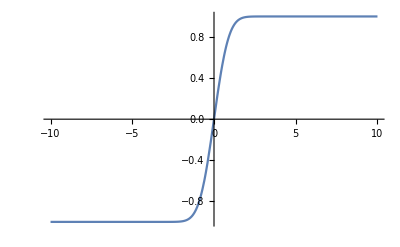

```mathematica
Plot[Erf[x],{x,-10,10}]
```

```mathematica
1/(1+ρ)+1/(1-ρ)//FullSimplify
```

-2/(-1+ρ^2)

```mathematica
Sin[t+π/2]==Cos[t]//FullSimplify
```

True

```mathematica
Cos[t+π/2]==-Sin[t]//FullSimplify
```

True

```mathematica
Sum[a^i b^(k-i),{i,0,k}]
```

(a^(1+k)-b^(1+k))/(a-b)

```mathematica
Manipulate[
ContourPlot[x^2+y^2-2ρ x y==c,{x,-1,1},{y,-1,1},PlotPoints->30,
Epilog->{Thick,Dashed,
Line[{{0,0},{√(c/(2(1+ρ))),-√(c/(2(1+ρ)))}}],Text["c/(1 + ρ)",{0.5 √(c/(2(1+ρ))),-0.8 √(c/(2(1+ρ)))}],
Line[{{0,0},{√(c/(2(1-ρ))),√(c/(2(1-ρ)))}}],Text["c/(1 - ρ)",{0.4 √(c/(2(1-ρ))),0.9 √(c/(2(1-ρ)))}]
}],

{{ρ,0},-1,1},{{c,0.5},0,1}]
```

```mathematica
(x1+a1)^2+(x2+a2)^2-2ρ(x1+a1)(x2+a2)//Expand
```

a1^2+a2^2+2 a1 x1+x1^2+2 a2 x2+x2^2-2 a1 a2 ρ-2 a2 x1 ρ-2 a1 x2 ρ-2 x1 x2 ρ

```mathematica
Manipulate[
StreamPlot[{x1-ρ x2,x2-ρ x1},{x1,-1,1},{x2,-1,1}],
{{ρ,0},-1,1}]
```

```mathematica
Inverse[1/(1-ρ^2)({{1, -ρ}, {-ρ, 1}})]//FullSimplify
```

{{1,ρ},{ρ,1}}

```mathematica
Inverse[({{1, Σ12/(√(Σ11 Σ22))}, {Σ12/(√(Σ11 Σ22)), 1}})]//FullSimplify
```

{{(Σ11 Σ22)/(-Σ12^2+Σ11 Σ22),(Σ12 √(Σ11 Σ22))/(Σ12^2-Σ11 Σ22)},{(Σ12 √(Σ11 Σ22))/(Σ12^2-Σ11 Σ22),(Σ11 Σ22)/(-Σ12^2+Σ11 Σ22)}}

```mathematica
Solve[(Σ11 Σ22)/(-Σ12^2+Σ11 Σ22)==1/(1-ρ^2),ρ]
```

{{ρ→-Σ12/(√Σ11 √Σ22)},{ρ→Σ12/(√Σ11 √Σ22)}}

```mathematica
Solve[(Σ12 √(Σ11 Σ22))/(Σ12^2-Σ11 Σ22)==ρ/(1-ρ^2),ρ]//FullSimplify
```

{{ρ→-Σ12/(√(Σ11 Σ22))},{ρ→(√(Σ11 Σ22))/Σ12}}

```mathematica
Inverse[({{Σ11, Σ12}, {Σ12, Σ22}})]//FullSimplify
```

{{Σ22/(-Σ12^2+Σ11 Σ22),Σ12/(Σ12^2-Σ11 Σ22)},{Σ12/(Σ12^2-Σ11 Σ22),Σ11/(-Σ12^2+Σ11 Σ22)}}

```mathematica
Det[{{Σ11, Σ12}, {Σ12, Σ22}}]
```

-Σ12^2+Σ11 Σ22

```mathematica
Inverse[{{1/(1-ρ^2), -ρ/(1-ρ^2)}, {-ρ/(1-ρ^2), 1/(1-ρ^2)}}]//FullSimplify//MatrixForm
```

(1 | ρ
ρ | 1)

```mathematica
Inverse[{{1, Σ12/(√(Σ11 Σ22))}, {Σ12/(√(Σ11 Σ22)), 1}}]//FullSimplify//MatrixForm
```

((Σ11 Σ22)/(-Σ12^2+Σ11 Σ22) | (Σ12 √(Σ11 Σ22))/(Σ12^2-Σ11 Σ22)
(Σ12 √(Σ11 Σ22))/(Σ12^2-Σ11 Σ22) | (Σ11 Σ22)/(-Σ12^2+Σ11 Σ22))

```mathematica
Solve[(Σ12 √(Σ11 Σ22))/(Σ12^2-Σ11 Σ22)==-ρ/(1-ρ^2),ρ]//FullSimplify
```

{{ρ→Σ12/(√(Σ11 Σ22))},{ρ→-(√(Σ11 Σ22))/Σ12}}

```mathematica
Module[{μ,Σ,a,b},
a={100,200};b={120,230};
μ={0,0};Σ=({{1, 9/10}, {9/10, 1}});
Plot3D[-1/2({x1,x2}-μ).Inverse[Σ].({x1,x2}-μ),{x1,119,120},{x2,200,201}]]
```

-Graphics3D-

```mathematica
Exp[-30200]/Exp[-29600]
```

1/ⅇ^600

```mathematica
Module[{ρ=0.5,a1=-0.5,a2=0.2,b1=-0.2,b2=1},
NIntegrate[Exp[-(x1^2+x2^2-2ρ x1 x2)/(2(1-ρ^2))]x1,{x1,a1,b1},{x2,a2,b2}]/NIntegrate[Exp[-(x1^2+x2^2-2ρ x1 x2)/(2(1-ρ^2))],{x1,a1,b1},{x2,a2,b2}]]
```

-0.343796

```mathematica
({x1,x2}).Inverse[{{1, ρ}, {ρ, 1}}].({x1,x2})//FullSimplify
```

(x1^2+x2^2-2 x1 x2 ρ)/(1-ρ^2)

```mathematica
Module[{μ,Σ,ρ=0.5,a1=-0.5,a2=0.2,b1=-0.2,b2=1},
μ={0,0};
Σ=({{1, ρ}, {ρ, 1}});
NIntegrate[Exp[-1/2({x1,x2}-μ).Inverse[Σ].({x1,x2}-μ)]x1,
{x1,a1,b1},{x2,a2,b2}]/NIntegrate[Exp[-1/2({x1,x2}-μ).Inverse[Σ].({x1,x2}-μ)],
{x1,a1,b1},{x2,a2,b2}]]
```

-0.343796

```mathematica
Module[{ρ=0.5,a1=-0.5,a2=0.2,b1=-0.2,b2=1},
NIntegrate[1/(2π √(1-ρ^2))Exp[-(x1^2+x2^2-2ρ x1 x2)/(2(1-ρ^2))],{x1,a1,b1},{x2,a2,b2}]]
```

```mathematica
0.02752462487030073f
```

```mathematica
0.004612694953630602f
```

```mathematica
Moment[TruncatedDistribution[{{-0.5,-0.2},{0.2,1}},MultinormalDistribution[{{1, 0.5}, {0.5, 1}}]],
{1,0}]
```

$Aborted

```mathematica
Eigenvalues[{{1, ρ}, {ρ, 1}}]
```

{1-ρ,1+ρ}

```mathematica
Eigenvectors[{{1, ρ}, {ρ, 1}}]
```

{{-1,1},{1,1}}

```mathematica
m
```

```mathematica
Det
```

```mathematica
Det[{{1/(1-ρ^2), ρ/(1-ρ^2)}, {ρ/(1-ρ^2), 1/(1-ρ^2)}}]//FullSimplify
```

1/(1-ρ^2)

```mathematica
Det[{{1/(1-ρ^2), ρ/(1-ρ^2)}, {ρ/(1-ρ^2), 1/(1-ρ^2)}}]//FullSimplify
```

```mathematica
Eigenvalues[{{2, -2ρ}, {-2ρ, 2}}]
```

{2 (1-ρ),2 (1+ρ)}

```mathematica
D[x^2+y^2-2ρ x y,{{x,y},2}]//MatrixForm
```

(2 | -2 ρ
-2 ρ | 2)

# Singular cases ρ=±1

```mathematica
FullSimplify[Integrate[Exp[-(x1+x2)^2],{x1,a1,b1},{x2,a2,b2},Assumptions->-∞<a1<a2<∞&&-∞<b1<b2<∞],-∞<a1<a2<∞&&-∞<b1<b2<∞]
```

$Aborted

```mathematica
FullSimplify[Integrate[Exp[-(x1+x2)^2]x1,{x1,a1,b1},{x2,a2,b2},Assumptions->-∞<a1<a2<∞&&-∞<b1<b2<∞],-∞<a1<a2<∞&&-∞<b1<b2<∞]
```

1/8 (2 (a1-a2) ⅇ^(-(a1+a2)^2)+2 (a2-b1) ⅇ^(-(a2+b1)^2)+2 (-a1+b2) ⅇ^(-(a1+b2)^2)+2 (b1-b2) ⅇ^(-(b1+b2)^2)+√π ((-1+2 a1^2-2 a2^2) Erf[a1+a2]+(1+2 a2^2-2 b1^2) Erf[a2+b1])+√π ((1-2 a1^2+2 b2^2) Erf[a1+b2]+(-1+2 b1^2-2 b2^2) Erf[b1+b2]))

```mathematica
FullSimplify[Integrate[Exp[-(x1+x2)^2] x1^2,{x1,a1,b1},{x2,a2,b2},Assumptions->-∞<a1<a2<∞&&-∞<b1<b2<∞],-∞<a1<a2<∞&&-∞<b1<b2<∞]
```

1/12 (2 (1+a1^2-a1 a2+a2^2) ⅇ^(-(a1+a2)^2)-2 (1+a2^2-a2 b1+b1^2) ⅇ^(-(a2+b1)^2)-2 (1+a1^2-a1 b2+b2^2) ⅇ^(-(a1+b2)^2)+2 (1+b1^2-b1 b2+b2^2) ⅇ^(-(b1+b2)^2)+(2 a1^3+3 a2+2 a2^3) √π Erf[a1+a2]-(3 a2+2 a2^3+2 b1^3) √π Erf[a2+b1]+√π (-(2 a1^3+3 b2+2 b2^3) Erf[a1+b2]+(2 b1^3+3 b2+2 b2^3) Erf[b1+b2]))

```mathematica
FullSimplify[Integrate[Exp[-(x1+x2)^2]x1 x2,{x1,a1,b1},{x2,a2,b2,Assumptions->-∞<a1<a2<∞&&-∞<b1<b2<∞}],-∞<a1<a2<∞&&-∞<b1<b2<∞]
```

1/12 (-2 (1+a1^2-a1 a2+a2^2) ⅇ^(-(a1+a2)^2)+2 (1+a2^2-a2 b1+b1^2) ⅇ^(-(a2+b1)^2)+2 (1+a1^2-a1 b2+b2^2) ⅇ^(-(a1+b2)^2)-2 (1+b1^2-b1 b2+b2^2) ⅇ^(-(b1+b2)^2)+3 (ⅇ^(-(a1+a2)^2)-ⅇ^(-(a2+b1)^2)+a2 √π (Erf[a1+a2]-Erf[a2+b1]))+√π (-(2 a1^3+3 a2+2 a2^3) Erf[a1+a2]+(3 a2+2 a2^3+2 b1^3) Erf[a2+b1])+(2 a1^3+3 b2+2 b2^3) √π Erf[a1+b2]-(2 b1^3+3 b2+2 b2^3) √π Erf[b1+b2]+3 (-ⅇ^(-(a1+b2)^2)+ⅇ^(-(b1+b2)^2)+b2 √π (-Erf[a1+b2]+Erf[b1+b2])))